# Relativistic free fall on a center.

## 1. Preliminaries : a constant force, F, acting on the particle.

```mathematica
Clear[x];DSolve[{D[(m D[x[t],t])/(√(1-D[x[t],t]^2/c^2)),t]==F,x[0]==0,x'[0]==0},x[t],t]
```

{{x[t]→(c √(c^2 m^2)-c √(c^2 m^2+F^2 t^2))/F},{x[t]→(-c √(c^2 m^2)+c √(c^2 m^2+F^2 t^2))/F}}

```mathematica
x[t_]:=(-c √(c^2 m^2)+c √(c^2 m^2+F^2 t^2))/F
```

```mathematica
v[t_]:=D[x[t],t]
```

```mathematica
v[t]
```

(c F t)/(√(c^2 m^2+F^2 t^2))

The velocity tends to the limit, c :

```mathematica
Limit[v[t],t->∞]//FullSimplify
```

(c F)/(√(F^2))

## 2. The (unrealistic) newtonian free fall.

```mathematica
Clear[r,v];equation=NDSolve[{D[D[r[t],t],t]==-10/r[t]^2,r[0]==1,r'[0]==0},r,{t,0,0.35}]
```

{{r→InterpolatingFunction[{{0.,0.35}},<>]}}

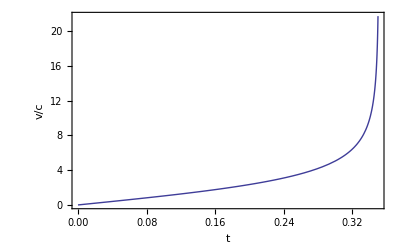

```mathematica
Plot[Evaluate[-r'[t]/.equation],{t,0,0.35},PlotStyle->Thick,LabelStyle->{Bold,Directive[14]},FrameLabel->{t,v/c},PlotRange->All,Frame->True]
```

## 3. The relativistic free fall.

The center is fixed. The point is initially at rest a a distance r[0]=1 (M=10, m_0=1, G=c=1, arbitrary units).

```mathematica
Clear[r,v];equation=NDSolve[{D[D[r[t],t]/(√(1-D[r[t],t]^2)),t]==-(10/√(1-D[r[t],t]^2))/r[t]^2,r[0]==1,r'[0]==0},r,{t,0,1.07}]
```

{{r→InterpolatingFunction[{{0.,1.07}},<>]}}

Position versus time :

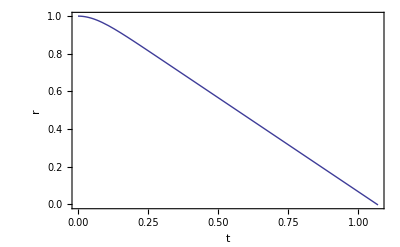

```mathematica
Plot[Evaluate[r[t]/.equation],{t,0,1.07},PlotStyle->Thick,LabelStyle->{Bold,Directive[14]},FrameLabel->{t,r},PlotRange->All,Frame->True]
```

Velocity versus time :

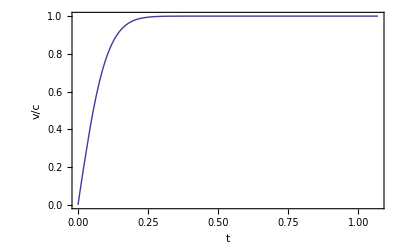

```mathematica
Plot[Evaluate[-r'[t]/.equation],{t,0,1.07},PlotStyle->Thick,LabelStyle->{Bold,Directive[14]},FrameLabel->{t,v/c},PlotRange->All,Frame->True]
```